### Importing csv file

```mathematica
a =SemanticImport["~/Downloads/Feral cat (Felis catus) - Scotia, NSW.csv",HeaderLines->1,Delimiters->","]
```

### Importing columns from csv file

```mathematica
Import["~/Downloads/FeralCatNSW.csv"][[All,{4,5}]]
```

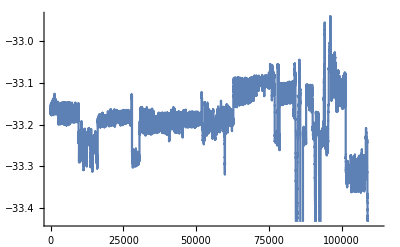

```mathematica
xlong =Import["~/Downloads/FeralCatNSW.csv", {"Data",All,4}];
ylat =Import["~/Downloads/FeralCatNSW.csv", {"Data",All,5}];
ListLinePlot[ylat]
```

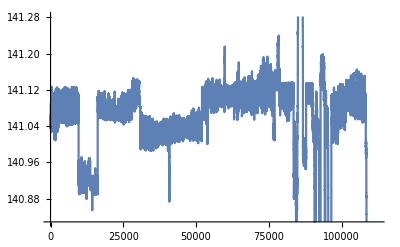

```mathematica
ListLinePlot[xlong]
```

### Plot x and y data

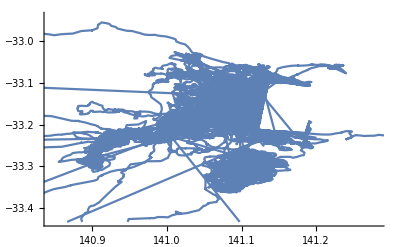

```mathematica
ListLinePlot[Transpose[{xlong,xlat}]]
```

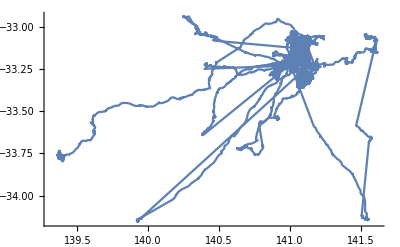

```mathematica
ListLinePlot[Transpose[{xlong,xlat}],PlotRange->All]
```

#### Sub-selection of data

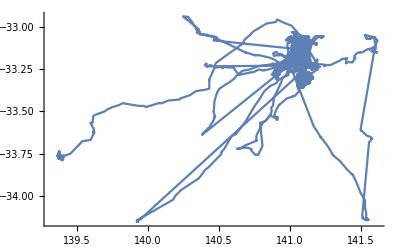

```mathematica
ListLinePlot[Transpose[{xlong[[1;;-1;;10]],xlat[[1;;-1;;10]]}],PlotRange->All]
```

```mathematica
zf = Import["/Users/eric/Downloads/MBL/Birdsong2008/BirdLec/monster/zfinch.wav"];
```

```mathematica
Spectrogram[zf,512,128,ColorFunction->"SolarColors"]
```

-Graphics-

### Import XY at same time

```mathematica
xy =Import["~/Downloads/FeralCatNSW.csv", {"Data",All,{4,5}}];
```

```mathematica
ListLinePlot[xy]
```

-Graphics-